## Replicate control loop going out of bounds

```mathematica
u0 = {
0.75,
0.25,
0,
0.49 ,
-0.755,
0,
0,
0,
0,
0,
0,
0,
0,
0
};
u0 //MatrixForm
```

(0.75
0.25
0
0.49
-0.755
0
0
0
0
0
0
0
0
0)

```mathematica
J0 = IdentityMatrix[14];
J0 // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
F0 ={
0.815049,
0.295573,
-0.00468354,
0.455776,
-0.704523,
3.2728 10^(-6),
6.79598 10^(-5),
-0.00130128,
-2.8193334060944847 10^-01,
-5.6265770286976144 10^-02,
-1.7766117204476778 10^-03,
2.6404330778885838 10^(-3),
-5.4334436470262308 10^(-3),
1.8000997438485841 10^(-4)
}-u0;
F0 // MatrixForm
```

(0.065049
0.045573
-0.00468354
-0.034224
0.050477
3.2728×10^-6
0.0000679598
-0.00130128
-0.281933
-0.0562658
-0.00177661
0.00264043
-0.00543344
0.00018001)

```mathematica
Du1 = - Inverse[J0] . F0;
Du1 // MatrixForm
```

(-0.065049
-0.045573
0.00468354
0.034224
-0.050477
-3.2728×10^-6
-0.0000679598
0.00130128
0.281933
0.0562658
0.00177661
-0.00264043
0.00543344
-0.00018001)

```mathematica
u1 = u0 + Du1;
u1 // MatrixForm
```

(0.684951
0.204427
0.00468354
0.524224
-0.805477
-3.2728×10^-6
-0.0000679598
0.00130128
0.281933
0.0562658
0.00177661
-0.00264043
0.00543344
-0.00018001)

```mathematica
F1 = {
0.628324,
0.234822,
-0.000101189,
0.505433,
-0.781155,
-1.98738 10^(-6),
-2.74703 10^(-5),
0.000427619,
-3.7810363001392761 10^-01,
-7.4800325876886592 10^-03,
5.1451948294718090 10^-04,
-8.4072611575470256 10^-04,
-1.0358674191635216 10^-03,
-9.1276426996566928 10^-05
}-u0;
F1 // MatrixForm
```

(-0.121676
-0.015178
-0.000101189
0.015433
-0.026155
-1.98738×10^-6
-0.0000274703
0.000427619
-0.378104
-0.00748003
0.000514519
-0.000840726
-0.00103587
-0.0000912764)

```mathematica
J1 = J0 + Outer[Times, F1, Du1]/(Du1 . Du1);
J1 //MatrixForm
```

(1.08534 | 0.0597904 | -0.00614466 | -0.0449008 | 0.0662243 | 4.29381×10^-6 | 0.0000891612 | -0.00170724 | -0.369888 | -0.0738189 | -0.00233086 | 0.00346417 | -0.00712851 | 0.000236168
0.0106457 | 1.00746 | -0.000766492 | -0.00560098 | 0.00826089 | 5.35615×10^-7 | 0.0000111221 | -0.000212963 | -0.0461402 | -0.00920826 | -0.000290754 | 0.000432124 | -0.000889218 | 0.0000294598
0.0000709729 | 0.0000497233 | 0.999995 | -0.0000373407 | 0.0000550739 | 3.57085×10^-9 | 7.41488×10^-8 | -1.41979×10^-6 | -0.000307609 | -0.0000613898 | -1.9384×10^-6 | 2.88089×10^-6 | -5.92826×10^-6 | 1.96403×10^-7
-0.0108245 | -0.00758362 | 0.000779369 | 1.0057 | -0.00839968 | -5.44614×10^-7 | -0.0000113089 | 0.000216541 | 0.0469154 | 0.00936296 | 0.000295639 | -0.000439384 | 0.000904158 | -0.0000299547
0.0183448 | 0.0128523 | -0.00132083 | -0.00965171 | 1.01424 | 9.22981×10^-7 | 0.0000191657 | -0.000366981 | -0.0795096 | -0.0158678 | -0.000501033 | 0.000744644 | -0.00153232 | 0.0000507657
1.39393×10^-6 | 9.76579×10^-7 | -1.00363×10^-7 | -7.33382×10^-7 | 1.08167×10^-6 | 1. | 1.4563×10^-9 | -2.7885×10^-8 | -6.04152×10^-6 | -1.20571×10^-6 | -3.80708×10^-8 | 5.65815×10^-8 | -1.16433×10^-7 | 3.85741×10^-9
0.0000192674 | 0.0000134986 | -1.38725×10^-6 | -0.0000101371 | 0.0000149512 | 9.69397×10^-10 | 1. | -3.85436×10^-7 | -0.0000835081 | -0.0000166658 | -5.26229×10^-7 | 7.82091×10^-7 | -1.60937×10^-6 | 5.33186×10^-8
-0.000299927 | -0.000210128 | 0.0000215948 | 0.0001578 | -0.000232739 | -1.50902×10^-8 | -3.13349×10^-7 | 1.00001 | 0.00129994 | 0.00025943 | 8.19159×10^-6 | -0.0000121745 | 0.0000250525 | -8.29989×10^-7
0.265198 | 0.185796 | -0.0190943 | -0.139528 | 0.205789 | 0.0000133429 | 0.000277065 | -0.00530518 | -0.149413 | -0.22939 | -0.00724306 | 0.0107648 | -0.0221516 | 0.000733882
0.00524642 | 0.00367561 | -0.000377743 | -0.00276028 | 0.00407114 | 2.63962×10^-7 | 5.48118×10^-6 | -0.000104953 | -0.0227389 | 0.995462 | -0.00014329 | 0.00021296 | -0.000438225 | 0.0000145184
-0.000360879 | -0.00025283 | 0.0000259833 | 0.000189868 | -0.000280036 | -1.81568×10^-8 | -3.77027×10^-7 | 7.21924×10^-6 | 0.00156411 | 0.000312151 | 1.00001 | -0.0000146486 | 0.0000301436 | -9.98659×10^-7
0.000589677 | 0.000413124 | -0.0000424568 | -0.000310244 | 0.00045758 | 2.96683×10^-8 | 6.16063×10^-7 | -0.0000117962 | -0.00255576 | -0.000510056 | -0.0000161052 | 1.00002 | -0.0000492548 | 1.63181×10^-6
0.000726547 | 0.000509015 | -0.0000523115 | -0.000382255 | 0.000563789 | 3.65546×10^-8 | 7.59058×10^-7 | -0.0000145343 | -0.00314898 | -0.000628445 | -0.0000198434 | 0.0000294916 | 0.999939 | 2.01057×10^-6
0.0000640203 | 0.0000448523 | -4.60948×10^-6 | -0.0000336828 | 0.0000496788 | 3.22104×10^-9 | 6.68851×10^-8 | -1.2807×10^-6 | -0.000277475 | -0.000055376 | -1.74852×10^-6 | 2.59868×10^-6 | -5.34752×10^-6 | 1.)

Note: The Jacobian CoM elements are the largest off-diagonal terms

```mathematica
Du2 = - Inverse[J1] . F1;
Du2 // MatrixForm
```

(-2.95005
-0.367992
-0.00245334
0.374175
-0.634131
-0.0000481843
-0.00066602
0.0103677
-9.16716
-0.181354
0.0124746
-0.0203835
-0.0251147
-0.00221301)

```mathematica
u2 = u1 + Du2;
u2 // MatrixForm
```

(-2.2651
-0.163565
0.0022302
0.898399
-1.43961
-0.0000514571
-0.00073398
0.011669
-8.88523
-0.125088
0.0142512
-0.0230239
-0.0196813
-0.00239302)

Note: this is off-bounds!

## What if we ignore CoM updates?

```mathematica
Du1Test = Du1;
Du1Test[[9]] = 0;
Du1Test[[10]] = 0;
Du1Test[[11]] = 0;
Du1Test // MatrixForm
```

(-0.065049
-0.045573
0.00468354
0.034224
-0.050477
-3.2728×10^-6
-0.0000679598
0.00130128
0
0
0
-0.00264043
0.00543344
-0.00018001)

```mathematica
u1Test = u0 + Du1Test;
u1Test // MatrixForm
```

(0.684951
0.204427
0.00468354
0.524224
-0.805477
-3.2728×10^-6
-0.0000679598
0.00130128
0
0
0
-0.00264043
0.00543344
-0.00018001)

```mathematica
F1Test = F1;
F1Test[[9]] = 0;
F1Test[[10]] = 0;
F1Test[[11]] = 0;
F1Test // MatrixForm
```

(-0.121676
-0.015178
-0.000101189
0.015433
-0.026155
-1.98738×10^-6
-0.0000274703
0.000427619
0
0
0
-0.000840726
-0.00103587
-0.0000912764)

```mathematica
J1Test = J0 + Outer[Times, F1Test, Du1Test]/(Du1Test . Du1Test);
J1Test //MatrixForm
```

(1.78461 | 0.549696 | -0.0564923 | -0.412806 | 0.608848 | 0.0000394762 | 0.000819724 | -0.0156959 | 0. | 0. | 0. | 0.0318486 | -0.0655376 | 0.00217126
0.0978736 | 1.06857 | -0.00704692 | -0.0514939 | 0.0759484 | 4.9243×10^-6 | 0.000102253 | -0.00195792 | 0. | 0. | 0. | 0.00397283 | -0.00817523 | 0.000270845
0.000652506 | 0.000457142 | 0.999953 | -0.000343301 | 0.000506334 | 3.28294×10^-8 | 6.81704×10^-7 | -0.0000130531 | 0. | 0. | 0. | 0.0000264862 | -0.0000545028 | 1.80568×10^-6
-0.0995179 | -0.0697218 | 0.00716531 | 1.05236 | -0.0772244 | -5.00703×10^-6 | -0.000103971 | 0.00199082 | 0. | 0. | 0. | -0.00403958 | 0.00831258 | -0.000275396
0.168658 | 0.118161 | -0.0121434 | -0.0887352 | 1.13088 | 8.48564×10^-6 | 0.000176205 | -0.00337393 | 0. | 0. | 0. | 0.00684605 | -0.0140877 | 0.000466726
0.0000128154 | 8.9784×10^-6 | -9.22711×10^-7 | -6.74252×10^-6 | 9.94454×10^-6 | 1. | 1.33889×10^-8 | -2.56367×10^-7 | 0. | 0. | 0. | 5.20195×10^-7 | -1.07045×10^-6 | 3.5464×10^-8
0.000177139 | 0.000124103 | -0.000012754 | -0.0000931976 | 0.000137457 | 8.91237×10^-9 | 1. | -3.5436×10^-6 | 0. | 0. | 0. | 7.19033×10^-6 | -0.0000147962 | 4.90197×10^-7
-0.00275745 | -0.00193186 | 0.000198537 | 0.00145077 | -0.00213974 | -1.38735×10^-7 | -2.88084×10^-6 | 1.00006 | 0. | 0. | 0. | -0.000111929 | 0.000230326 | -7.63069×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0.00542133 | 0.00379815 | -0.000390337 | -0.0028523 | 0.00420686 | 2.72762×10^-7 | 5.66392×10^-6 | -0.000108452 | 0. | 0. | 0. | 1.00022 | -0.000452835 | 0.0000150024
0.00667967 | 0.00467975 | -0.000480938 | -0.00351435 | 0.00518332 | 3.36073×10^-7 | 6.97857×10^-6 | -0.000133624 | 0. | 0. | 0. | 0.000271138 | 0.999442 | 0.0000184846
0.000588586 | 0.00041236 | -0.0000423783 | -0.00030967 | 0.000456733 | 2.96134×10^-8 | 6.14924×10^-7 | -0.0000117744 | 0. | 0. | 0. | 0.0000238915 | -0.0000491637 | 1.)

```mathematica
Du2Test = - Inverse[J1Test] . F1Test;
Du2Test // MatrixForm
```

(0.0597596
0.00745448
0.0000496977
-0.00757972
0.0128457
9.76077×10^-7
0.0000134917
-0.00021002
0.
0.
0.
0.000412912
0.000508753
0.0000448293)

```mathematica
u2Test = u1Test + Du2Test;
u2Test // MatrixForm
```

(0.744711
0.211881
0.00473324
0.516644
-0.792631
-2.29672×10^-6
-0.0000544681
0.00109126
0.
0.
0.
-0.00222752
0.0059422
-0.000135181)

Note: this is within the proper bounds!

## Analyze inverse Jacobians

```mathematica
Inverse[J1] // MatrixForm
```

(3.06913 | 1.44962 | -0.148978 | -1.08863 | 1.60561 | 0.000104104 | 0.00216172 | -0.0413922 | -8.96797 | -1.78975 | -0.056512 | 0.0839891 | -0.172832 | 0.00572591
0.258106 | 1.18083 | -0.0185837 | -0.135796 | 0.200286 | 0.000012986 | 0.000269656 | -0.00516331 | -1.11867 | -0.223255 | -0.00704936 | 0.0104769 | -0.0215592 | 0.000714256
0.00172075 | 0.00120555 | 0.999876 | -0.00090533 | 0.00133527 | 8.65756×10^-8 | 1.79775×10^-6 | -0.0000344229 | -0.007458 | -0.0014884 | -0.0000469968 | 0.0000698476 | -0.000143731 | 4.76182×10^-6
-0.262442 | -0.183866 | 0.0188959 | 1.13808 | -0.203651 | -0.0000132042 | -0.000274186 | 0.00525006 | 1.13747 | 0.227006 | 0.0071678 | -0.0106529 | 0.0219214 | -0.000726256
0.444773 | 0.311606 | -0.0320237 | -0.234007 | 1.34514 | 0.0000223778 | 0.000464675 | -0.00889751 | -1.92772 | -0.384717 | -0.0121476 | 0.018054 | -0.0371512 | 0.00123082
0.0000337959 | 0.0000236773 | -2.43331×10^-6 | -0.0000177809 | 0.0000262251 | 1. | 3.53082×10^-8 | -6.76074×10^-7 | -0.000146477 | -0.0000292326 | -9.23031×10^-7 | 1.37183×10^-6 | -2.82292×10^-6 | 9.35234×10^-8
0.00046714 | 0.000327276 | -0.0000336342 | -0.000245775 | 0.000362493 | 2.35031×10^-8 | 1. | -9.34495×10^-6 | -0.00202466 | -0.000404064 | -0.0000127585 | 0.0000189619 | -0.0000390195 | 1.29272×10^-6
-0.00727178 | -0.00509457 | 0.000523569 | 0.00382587 | -0.00564278 | -3.65864×10^-7 | -7.59717×10^-6 | 1.00015 | 0.0315171 | 0.00628991 | 0.000198606 | -0.000295172 | 0.0006074 | -0.0000201232
6.42975 | 4.50465 | -0.462943 | -3.38286 | 4.98939 | 0.000323499 | 0.00671747 | -0.128625 | -26.8676 | -5.56158 | -0.175609 | 0.260993 | -0.537067 | 0.017793
0.1272 | 0.0891156 | -0.00915842 | -0.0669233 | 0.0987052 | 6.39979×10^-6 | 0.000132892 | -0.00254459 | -0.551306 | 0.889975 | -0.00347407 | 0.00516323 | -0.0106248 | 0.000352
-0.00874954 | -0.00612988 | 0.000629969 | 0.00460337 | -0.00678951 | -4.40214×10^-7 | -9.14106×10^-6 | 0.000175031 | 0.037922 | 0.00756814 | 1.00024 | -0.000355157 | 0.000730836 | -0.0000242126
0.0142968 | 0.0100162 | -0.00102937 | -0.00752191 | 0.0110941 | 7.19311×10^-7 | 0.0000149365 | -0.000286001 | -0.0619646 | -0.0123664 | -0.000390472 | 1.00058 | -0.00119419 | 0.0000395634
0.0176152 | 0.0123411 | -0.0012683 | -0.00926782 | 0.0136691 | 8.86271×10^-7 | 0.0000184034 | -0.000352385 | -0.0763473 | -0.0152367 | -0.000481105 | 0.000715027 | 0.998529 | 0.0000487465
0.00155218 | 0.00108745 | -0.000111757 | -0.000816643 | 0.00120447 | 7.80946×10^-8 | 1.62164×10^-6 | -0.0000310508 | -0.00672741 | -0.0013426 | -0.000042393 | 0.0000630052 | -0.000129651 | 1.)

```mathematica
Inverse[J1Test] // MatrixForm
```

(0.614647 | -0.269976 | 0.0277455 | 0.202744 | -0.299028 | -0.0000193882 | -0.000402597 | 0.00770884 | 0. | 0. | 0. | -0.015642 | 0.032188 | -0.00106639
-0.0480694 | 0.966323 | 0.003461 | 0.0252906 | -0.0373011 | -2.41851×10^-6 | -0.0000502204 | 0.000961609 | 0. | 0. | 0. | -0.00195121 | 0.00401516 | -0.000133022
-0.00032047 | -0.00022452 | 1.00002 | 0.000168608 | -0.00024868 | -1.61238×10^-8 | -3.3481×10^-7 | 6.41088×10^-6 | 0. | 0. | 0. | -0.0000130083 | 0.0000267684 | -8.86836×10^-7
0.048877 | 0.034243 | -0.00351915 | 0.974285 | 0.0379278 | 2.45914×10^-6 | 0.0000510641 | -0.000977765 | 0. | 0. | 0. | 0.00198399 | -0.00408262 | 0.000135257
-0.082834 | -0.0580331 | 0.00596406 | 0.0435812 | 0.935722 | -4.16761×10^-6 | -0.0000865407 | 0.00165706 | 0. | 0. | 0. | -0.00336235 | 0.006919 | -0.000229226
-6.29412×10^-6 | -4.40963×10^-6 | 4.53178×10^-7 | 3.3115×10^-6 | -4.88414×10^-6 | 1. | -6.57577×10^-9 | 1.25911×10^-7 | 0. | 0. | 0. | -2.55487×10^-7 | 5.25738×10^-7 | -1.74177×10^-8
-0.0000869996 | -0.0000609515 | 6.26399×10^-6 | 0.0000457728 | -0.0000675103 | -4.3772×10^-9 | 1. | 1.74039×10^-6 | 0. | 0. | 0. | -3.53144×10^-6 | 7.26695×10^-6 | -2.40754×10^-7
0.00135429 | 0.000948807 | -0.000097509 | -0.000712527 | 0.00105091 | 6.81381×10^-8 | 1.41489×10^-6 | 0.999973 | 0. | 0. | 0. | 0.0000549725 | -0.000113122 | 3.74772×10^-6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
-0.00266262 | -0.00186542 | 0.000191709 | 0.00140087 | -0.00206615 | -1.33964×10^-7 | -2.78176×10^-6 | 0.0000532646 | 0. | 0. | 0. | 0.999892 | 0.000222404 | -7.36825×10^-6
-0.00328064 | -0.0022984 | 0.000236206 | 0.00172603 | -0.00254572 | -1.65058×10^-7 | -3.42744×10^-6 | 0.0000656279 | 0. | 0. | 0. | -0.000133166 | 1.00027 | -9.0785×10^-6
-0.000289076 | -0.000202525 | 0.0000208136 | 0.000152091 | -0.000224319 | -1.45443×10^-8 | -3.02012×10^-7 | 5.78286×10^-6 | 0. | 0. | 0. | -0.000011734 | 0.0000241461 | 0.999999)

## What if we damp the Jacobian initially?

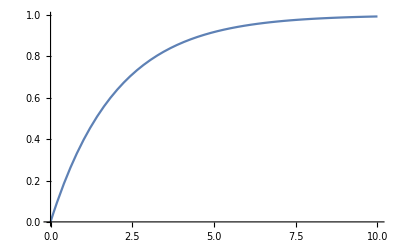

```mathematica
dampingParam[k_] := 1 - Exp[-k/2];
Plot[dampingParam[k], {k, 0, 10}, AxesOrigin->{0,0}]
```

```mathematica
Du1Damped = - dampingParam[1] Inverse[J0] . F0;
u1Damped = u0 + Du1Damped;
u1Damped // MatrixForm
```

(0.724405
0.232068
0.00184283
0.503466
-0.774861
-1.28775×10^-6
-0.0000267401
0.000512014
0.110932
0.0221389
0.000699042
-0.00103893
0.00213789
-0.0000708284)

```mathematica
Du2Damped = - dampingParam[1] Inverse[J1] . F1;
u2Damped = u1 + Du2Damped;
u2Damped // MatrixForm
```

(-0.475803
0.0596333
0.00371823
0.67145
-1.05499
-0.0000222318
-0.000330018
0.00538064
-3.32506
-0.0150916
0.00668498
-0.0106607
-0.00444843
-0.00105076)